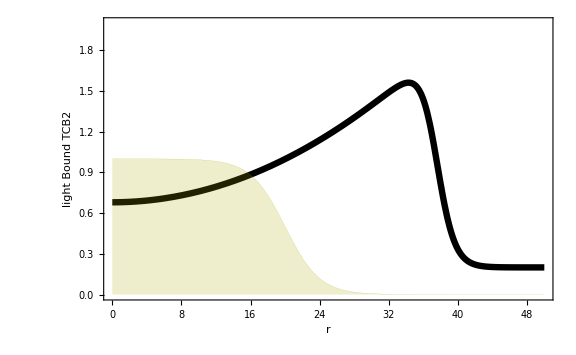

```mathematica
ClearAll["Global`*"];


SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.003]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->26}];


spaceFunc[r_,r0_,s_]:=1/2*(1-Tanh[(r-r0)/s]);
f[r_,r0_,s_,flat_,aOff_,Cscale_]:=Cscale*(1-flat)*spaceFunc[r,r0,s]*(aOff+(1-aOff)*(r/r0)^2) +flat;

Cscale = 2;
aOff = 0.3;
r0Base = 37.5;
sBase = 2;
r0 = 20;
flat = 0.2;
s = 4;

ylabel = Row[{Text[Style["light",Darker@Yellow]],"  Bound TCB2"}];
Show[
Plot[f[r,r0Base,sBase,flat,aOff,Cscale],{r,0,50},PlotRange->{0,2},PlotStyle->Directive[Black,Thickness[0.008]],Frame->{{True,False},{True,False}},Axes->False,(*LabelStyle->Opacity[0],*)FrameTicks->None,ImageSize->Large,FrameLabel->{"r",ylabel}],
Plot[spaceFunc[r,r0,s],{r,0,50},PlotRange->{0,2},Filling->Axis,PlotStyle->Directive[Thickness[0.0001],Darker@Yellow]]
]
```